```mathematica
knownGraphs=Map[{ChromaticPolynomial[Graph[GraphData[#]],x],#}&,Select[Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&],VertexCount[GraphData[#]]<10&]]
```

{{2 x-3 x^2+x^3,TriangleGraph},{-6 x+11 x^2-6 x^3+x^4,TetrahedralGraph},{18 x-39 x^2+29 x^3-9 x^4+x^5,{JohnsonSkeleton,12}},{-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6,OctahedralGraph},{-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6,{Hexahedral,5}},{210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7,{JohnsonSkeleton,13}},{192 x-526 x^2+565 x^3-311 x^4+94 x^5-15 x^6+x^7,{Heptahedral,34}},{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,{Heptahedral,29}},{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,{Heptahedral,15}},{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,{Apollonian,2}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,14}}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,12}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,11}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,10}}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,9}}},{-630 x+1905 x^2-2347 x^3+1554 x^4-605 x^5+140 x^6-18 x^7+x^8,{Triangulated,{8,8}}},{-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8,{Triangulated,{8,7}}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,6}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,5}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,4}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,3}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,2}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,TriakisTetrahedralGraph},{-714 x+2107 x^2-2525 x^3+1627 x^4-619 x^5+141 x^6-18 x^7+x^8,{JohnsonSkeleton,84}},{2532 x-8062 x^2+10722 x^3-7932 x^4+3625 x^5-1061 x^6+196 x^7-21 x^8+x^9,FritschGraph}}

```mathematica
FindKnowngraph[graph_]:=Module[
{pols, found},
pols = ChromaticPolynomial[graph,x];
found = Select[knownGraphs,#[[1]]==pols&];
If[Length[found]==1,
Return[found[[1]][[2]]],
Return[pols]
];
]
```

```mathematica
Map[{ChromaticPolynomial[Graph[GraphData[#]],x],#}&,Select[Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&],VertexCount[GraphData[#]]<10&]]
```

{{2 x-3 x^2+x^3,TriangleGraph},{-6 x+11 x^2-6 x^3+x^4,TetrahedralGraph},{18 x-39 x^2+29 x^3-9 x^4+x^5,{JohnsonSkeleton,12}},{-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6,OctahedralGraph},{-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6,{Hexahedral,5}},{210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7,{JohnsonSkeleton,13}},{192 x-526 x^2+565 x^3-311 x^4+94 x^5-15 x^6+x^7,{Heptahedral,34}},{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,{Heptahedral,29}},{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,{Heptahedral,15}},{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,{Apollonian,2}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,14}}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,12}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,11}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,10}}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,9}}},{-630 x+1905 x^2-2347 x^3+1554 x^4-605 x^5+140 x^6-18 x^7+x^8,{Triangulated,{8,8}}},{-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8,{Triangulated,{8,7}}},{-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,{Triangulated,{8,6}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,5}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,4}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,3}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,{Triangulated,{8,2}}},{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,TriakisTetrahedralGraph},{-714 x+2107 x^2-2525 x^3+1627 x^4-619 x^5+141 x^6-18 x^7+x^8,{JohnsonSkeleton,84}},{2532 x-8062 x^2+10722 x^3-7932 x^4+3625 x^5-1061 x^6+196 x^7-21 x^8+x^9,FritschGraph}}

```mathematica
Select[knownGraphs,#[[1]]==ChromaticPolynomial[Graph[{1<->3,2<->3,3<->1}],x]&]
```

{}



```mathematica
Graph[GraphData["TriangleGraph"]]
```

```mathematica
Graph[{1<->3,2<->3,3<->1}]
```

-Graphics-

```mathematica
ChromaticPolynomial[Graph[{1<->2,2<->3,3<->1}],x]
```

2 x-3 x^2+x^3

```mathematica
FindKnowngraph[Graph[{1<->2,2<->3,3<->1}]]
```

TriangleGraph

```mathematica
MyGraph[nodes_,edges_,opts___]:=Row[{Graph[nodes,edges, ImageSize->100,opts],Text[ FindKnowngraph[Graph[edges]]]}]
```

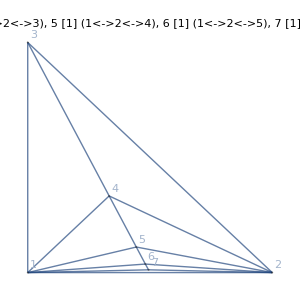
Row[-Graphics-,162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7]

```mathematica
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{49.4,1.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (1<->2<->6)"]
```

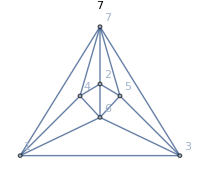
```mathematica
ChromaticPolynomial[-Graphics-,x]
```

ChromaticPolynomial::graph: A graph object is expected at position 1 in GraphicsBox[List[List[Hue[0.6`, 0.7`, 0.5`], Opacity[0.7`], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]], List[Arrowheads[0.`], ArrowBox[List[List[Skeleton[2]], List[Skeleton[2]]], 0.020399597244776385`]]], List[Hue[0.6`, 0.2`, 0.8`], EdgeForm[List[GrayLevel[0], Opacity[0.7`]]], List[DiskBox[List[-0.8660254037844387`, -0.4999999999999998`], 0.020399597244776385`], InsetBox[BoxData[FormBox[.

```mathematica
ChromaticPolynomial[Graph[Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&][[5]]],x]
```

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[Graph[{"Hexahedral", 5}], x].

```mathematica
Graph[Take[Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&],10]]
```

Graph[{TriangleGraph,TetrahedralGraph,{JohnsonSkeleton,12},OctahedralGraph,{Hexahedral,5},{JohnsonSkeleton,13},{Heptahedral,34},{Heptahedral,29},{Heptahedral,15},{Apollonian,2}}]

```mathematica
Take[Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&],10]
```

{TriangleGraph,TetrahedralGraph,{JohnsonSkeleton,12},OctahedralGraph,{Hexahedral,5},{JohnsonSkeleton,13},{Heptahedral,34},{Heptahedral,29},{Heptahedral,15},{Apollonian,2}}

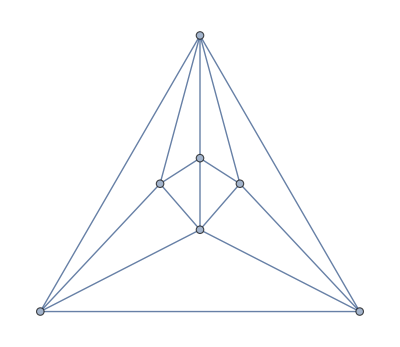

```mathematica
Graph[GraphData[{"JohnsonSkeleton",13}]]
```

```mathematica
ChromaticPolynomial[Graph[GraphData[{"JohnsonSkeleton",13}]],x]
```

210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7

```mathematica
Graph["OctahedralGraph"]
```

Graph[OctahedralGraph]

```mathematica
FullSimplify[162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7==162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7]
```

True

```mathematica
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{49.4,1.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{30.9,4.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{64.2,4.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,2<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6,3<->7,4<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,2<->6,5<->6,1<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,1<->6,2<->6,5<->6,2<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,1<->6,2<->6,5<->6,4<->7,5<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,5<->6,1<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{24.1,1.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,5<->6,2<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{74.1,1.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{48.1,3.7},7->{46.3,7.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->2<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,1<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,2<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6,3<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,3<->6,4<->6,1<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,1<->6,3<->6,4<->6,2<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,1<->6,3<->6,4<->6,4<->7,5<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,4<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{11.1,44.4},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{19.8,16.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{23.5,8.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{34.6,19.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,1<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,2<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,3<->7,4<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,4<->6,5<->6,1<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,1<->6,4<->6,5<->6,2<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,1<->6,4<->6,5<->6,4<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,4<->6,5<->6,1<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{13.0,7.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,5<->6,4<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{29.6,24.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{25.9,14.8},7->{35.2,13.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (1<->4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,1<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,2<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->6,3<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,2<->6,3<->6,4<->6,1<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,3<->6,4<->6,2<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,2<->6,3<->6,4<->6,4<->7,5<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,3<->6,4<->6,2<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,4<->7,6<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{44.4,44.4},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{64.2,16.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{67.9,8.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{45.7,19.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,1<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,2<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,3<->7,4<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,2<->6,4<->6,5<->6,1<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,4<->6,5<->6,2<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,2<->6,4<->6,5<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,4<->6,5<->6,2<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{79.6,7.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,5<->6,4<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{46.3,24.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{59.3,14.8},7->{51.9,13.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [1] (2<->4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{5.6,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{20.4,9.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{16.7,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{31.5,20.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,2<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,3<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,4<->5,1<->6,4<->6,3<->6,5<->6,1<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,4<->5,1<->6,4<->6,3<->6,5<->6,2<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,1<->6,4<->6,3<->6,5<->6,4<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,4<->6,3<->6,5<->6,1<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{8.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,3<->6,5<->6,4<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{25.0,25.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,5<->6,3<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{8.3,58.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,4<->6,3<->6,5<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,16.7},7->{30.6,13.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->4), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{55.6,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{70.4,9.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{33.3,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{48.1,20.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,1<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,3<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,4<->5,2<->6,4<->6,3<->6,5<->6,1<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,4<->5,2<->6,4<->6,3<->6,5<->6,2<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,2<->6,4<->6,3<->6,5<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,4<->6,3<->6,5<->6,2<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{83.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,3<->6,5<->6,4<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{50.0,25.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,5<->6,3<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{33.3,58.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->5,2<->6,4<->6,3<->6,5<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{66.7,16.7},7->{55.6,13.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->4), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{5.6,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{16.7,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{38.9,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{50.0,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,1<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,2<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,4<->5,3<->6,4<->6,1<->6,2<->6,1<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,4<->5,3<->6,4<->6,1<->6,2<->6,2<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,3<->6,4<->6,1<->6,2<->6,4<->7,5<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,4<->6,1<->6,2<->6,3<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{8.3,83.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,1<->6,2<->6,4<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{25.0,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,2<->6,1<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{8.3,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->5,3<->6,4<->6,1<->6,2<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{16.7,66.7},7->{58.3,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (3<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{40.7,1.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{18.5,13.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{55.6,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{33.3,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,1<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,2<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->6,3<->7,4<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,4<->5,1<->6,5<->6,2<->6,4<->6,2<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,1<->6,5<->6,2<->6,4<->6,4<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,5<->6,2<->6,4<->6,1<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{11.1,2.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,2<->6,4<->6,5<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{33.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,4<->6,2<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{61.1,2.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,5<->6,2<->6,4<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{22.2,5.6},7->{27.8,19.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (1<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{57.4,1.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{38.9,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{68.5,13.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{50.0,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,1<->7,4<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,2<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->6,3<->7,4<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,4<->5,2<->6,5<->6,1<->6,4<->6,1<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->6,5<->6,1<->6,4<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,5<->6,1<->6,4<->6,2<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{86.1,2.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,1<->6,4<->6,5<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{58.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,4<->6,1<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{36.1,2.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,5<->6,1<->6,4<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{72.2,5.6},7->{52.8,19.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (2<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,1<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (1<->2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{24.1,18.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{27.8,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{57.4,18.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{61.1,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,1<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,2<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->6,3<->7,4<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->6,5<->6,1<->6,2<->6,1<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->6,5<->6,1<->6,2<->6,2<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,5<->6,1<->6,2<->6,4<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{36.1,27.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,1<->6,2<->6,5<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{41.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,2<->6,1<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{19.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,2<->5,4<->6,5<->6,1<->6,2<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,11.1},6->{38.9,22.2},7->{69.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->2<->4), 6 [2] (4<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->6,3<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,1<->6,2<->6,4<->6,3<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,1<->6,2<->6,4<->6,4<->7,5<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,4<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,11.1},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->2<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{1.2,49.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{4.9,30.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{4.9,64.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,1<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,2<->7,4<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->6,3<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,3<->6,5<->6,1<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,1<->6,3<->6,5<->6,3<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,1<->6,3<->6,5<->6,4<->7,5<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,5<->6,1<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{1.9,24.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,5<->6,3<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{1.9,74.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,3<->6,5<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{3.7,48.1},7->{7.4,46.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->3<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{16.0,19.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{8.6,23.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{19.8,34.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,1<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,2<->7,4<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,3<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,4<->6,5<->6,1<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,1<->6,4<->6,5<->6,3<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,1<->6,4<->6,5<->6,4<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,4<->6,5<->6,1<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{7.4,13.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,5<->6,4<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{24.1,29.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,25.9},7->{13.0,35.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (1<->4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,1<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,2<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->6,3<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,3<->6,4<->6,1<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,2<->6,3<->6,4<->6,3<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,2<->6,3<->6,4<->6,4<->7,5<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,3<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,2<->6,3<->6,4<->7,6<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{44.4,44.4},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (2<->3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{16.0,64.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{8.6,67.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{19.8,45.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,4<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,3<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,4<->6,5<->6,3<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,3<->6,4<->6,5<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,4<->6,5<->6,3<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{7.4,79.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,5<->6,4<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{24.1,46.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{14.8,59.3},7->{13.0,51.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [1] (3<->4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{38.9,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{9.3,20.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{50.0,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{20.4,31.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,2<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,3<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,3<->5,4<->5,1<->6,4<->6,2<->6,5<->6,1<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,4<->5,1<->6,4<->6,2<->6,5<->6,3<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,1<->6,4<->6,2<->6,5<->6,4<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,4<->6,2<->6,5<->6,1<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{8.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,2<->6,5<->6,4<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{25.0,25.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,5<->6,2<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{58.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->5,1<->6,4<->6,2<->6,5<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,16.7},7->{13.9,30.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->4), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{55.6,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{33.3,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{55.6,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{33.3,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,1<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,3<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,3<->5,4<->5,2<->6,4<->6,1<->6,3<->6,1<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,4<->5,2<->6,4<->6,1<->6,3<->6,3<->7,5<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,2<->6,4<->6,1<->6,3<->6,4<->7,5<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,4<->6,1<->6,3<->6,2<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{83.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,1<->6,3<->6,4<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{50.0,25.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,3<->6,1<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{33.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->5,2<->6,4<->6,1<->6,3<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{66.7,16.7},7->{33.3,58.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (2<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{38.9,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{50.0,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{9.3,70.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{20.4,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,1<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,2<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->5,4<->5,3<->6,4<->6,2<->6,5<->6,1<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,4<->5,3<->6,4<->6,2<->6,5<->6,3<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,3<->6,4<->6,2<->6,5<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,4<->6,2<->6,5<->6,3<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{8.3,83.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,2<->6,5<->6,4<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{25.0,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{58.3,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->5,3<->6,4<->6,2<->6,5<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{16.7,66.7},7->{13.9,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->4), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{1.9,40.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{13.0,18.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{5.6,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{16.7,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,1<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,2<->7,4<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->6,3<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,4<->5,1<->6,5<->6,3<->6,4<->6,3<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,1<->6,5<->6,3<->6,4<->6,4<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,5<->6,3<->6,4<->6,1<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{2.8,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,3<->6,4<->6,5<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{8.3,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,4<->6,3<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{2.8,61.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,5<->6,3<->6,4<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,22.2},7->{19.4,27.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (1<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{1.9,57.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,1<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (1<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{5.6,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{13.0,68.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{16.7,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,1<->7,4<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,2<->7,4<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->6,3<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,4<->5,3<->6,5<->6,1<->6,4<->6,1<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->6,5<->6,1<->6,4<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,5<->6,1<->6,4<->6,3<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{2.8,86.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,1<->6,4<->6,5<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{8.3,58.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,4<->6,1<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{2.8,36.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->5,3<->6,5<->6,1<->6,4<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{5.6,72.2},7->{19.4,52.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (3<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,1<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (1<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{18.5,24.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,1<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{11.1,27.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (1<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,2<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{44.4,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (2<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{18.5,57.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{11.1,61.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,1<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,2<->7,4<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->6,3<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->6,5<->6,1<->6,3<->6,1<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (1<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,4<->6,5<->6,1<->6,3<->6,3<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,5<->6,1<->6,3<->6,4<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{27.8,36.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,1<->6,3<->6,5<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{16.7,41.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,3<->6,1<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{11.1,19.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,1<->5,3<->5,4<->6,5<->6,1<->6,3<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{11.1,44.4},6->{22.2,38.9},7->{11.1,69.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (1<->3<->4), 6 [2] (4<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{48.1,3.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{25.9,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{59.3,14.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,1<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->6,3<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,2<->6,4<->6,2<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,2<->6,4<->6,3<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,1<->6,2<->6,4<->6,4<->7,5<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{22.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{72.2,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,4<->7,6<->7,1<->7,2<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{44.4,11.1},7->{38.9,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->2<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{3.7,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{14.8,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{14.8,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,1<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,2<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->6,3<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,1<->6,3<->6,4<->6,2<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,1<->6,3<->6,4<->6,3<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,1<->6,3<->6,4<->6,4<->7,5<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{5.6,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,3<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{5.6,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,3<->6,4<->7,6<->7,1<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{11.1,44.4},7->{22.2,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (1<->3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{49.4,49.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{64.2,30.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{30.9,64.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,1<->7,4<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,2<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->6,3<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,3<->6,5<->6,2<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,2<->6,3<->6,5<->6,3<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,2<->6,3<->6,5<->6,4<->7,5<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,5<->6,2<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{74.1,24.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,5<->6,3<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{24.1,74.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,3<->6,5<->7,6<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{48.1,48.1},7->{46.3,46.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->3<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{64.2,19.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{67.9,23.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{45.7,34.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,1<->7,4<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,2<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,3<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,4<->6,5<->6,2<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,2<->6,4<->6,5<->6,3<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,2<->6,4<->6,5<->6,4<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,4<->6,5<->6,2<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{79.6,13.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,5<->6,4<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{46.3,29.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{59.3,25.9},7->{51.9,35.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (2<->4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{19.8,64.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{23.5,67.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{34.6,45.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,4<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,3<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,3<->6,4<->6,5<->6,2<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,4<->6,5<->6,3<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,3<->6,4<->6,5<->6,4<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,4<->6,5<->6,3<->7,6<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{13.0,79.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,5<->6,4<->7,6<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{29.6,46.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{25.9,59.3},7->{35.2,51.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [1] (3<->4<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{38.9,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{5.6,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{50.0,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{16.7,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,2<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,3<->7,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,3<->5,4<->5,1<->6,4<->6,2<->6,3<->6,2<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,4<->5,1<->6,4<->6,2<->6,3<->6,3<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,1<->6,4<->6,2<->6,3<->6,4<->7,5<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,4<->6,2<->6,3<->6,1<->7,6<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{8.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,2<->6,3<->6,4<->7,6<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{25.0,25.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,3<->6,2<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{58.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,3<->5,4<->5,1<->6,4<->6,2<->6,3<->7,6<->7,1<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,16.7},7->{8.3,58.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (1<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,1<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{55.6,5.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (1<->2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{33.3,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{70.4,20.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{48.1,31.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,1<->7,4<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,3<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,3<->5,4<->5,2<->6,4<->6,1<->6,5<->6,2<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,4<->5,2<->6,4<->6,1<->6,5<->6,3<->7,5<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,2<->6,4<->6,1<->6,5<->6,4<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,4<->6,1<->6,5<->6,2<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{83.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,1<->6,5<->6,4<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{50.0,25.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,5<->6,1<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{33.3,8.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,3<->5,4<->5,2<->6,4<->6,1<->6,5<->7,6<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{66.7,16.7},7->{55.6,30.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->4), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,1<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{5.6,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (1<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,1<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{16.7,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (1<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,2<->7,3<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{48.1,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (2<->3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{20.4,70.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{31.5,48.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,1<->7,4<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,2<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->5,4<->5,3<->6,4<->6,1<->6,5<->6,2<->7,5<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{72.2,22.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (2<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,4<->5,3<->6,4<->6,1<->6,5<->6,3<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,3<->6,4<->6,1<->6,5<->6,4<->7,5<->7,2<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,4<->6,1<->6,5<->6,3<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{8.3,83.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,1<->6,5<->6,4<->7,6<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{25.0,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,5<->6,1<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{8.3,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (1<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,3<->5,4<->5,3<->6,4<->6,1<->6,5<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{16.7,66.7},7->{30.6,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->4), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{57.4,40.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,2<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{68.5,18.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (2<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,3<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{25.9,59.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (3<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,3<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{38.9,55.6}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (3<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{50.0,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,1<->7,4<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,2<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->6,3<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,4<->5,2<->6,5<->6,3<->6,4<->6,3<->7,5<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{22.2,72.2}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (3<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,2<->6,5<->6,3<->6,4<->6,4<->7,5<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{38.9,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,5<->6,3<->6,4<->6,2<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{86.1,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (2<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,3<->6,4<->6,5<->7,6<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{58.3,33.3}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,4<->6,3<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{36.1,61.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,3<->5,4<->5,2<->6,5<->6,3<->6,4<->7,6<->7,2<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{72.2,22.2},7->{52.8,27.8}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (2<->5), 7 [2] (4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,1<->7,2<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{44.4,11.1}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (1<->2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,1<->7,3<->7,4<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{11.1,44.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (1<->3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,2<->7,3<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{40.7,57.4}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (2<->3<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,2<->7,4<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{59.3,25.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (2<->4<->5)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,2<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{55.6,38.9}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (2<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,3<->7,4<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{18.5,68.5}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (3<->4<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,4<->7,5<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{33.3,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [1] (4<->5<->6)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,2<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,1<->7,4<->7,2<->7,3<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{16.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [2] (1<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,3<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,2<->7,4<->7,1<->7,5<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{66.7,16.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [2] (2<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,2<->5,4<->5,3<->6,5<->6,2<->6,4<->6,3<->7,4<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{44.4,44.4},6->{22.2,72.2},7->{16.7,66.7}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [1] (2<->3<->4), 6 [2] (3<->5), 7 [2] (3<->4)"]
MyGraph[{1,2,3,4,5,6,7},{1<-
```

```mathematica
MyGraph[{1,2,3,4,5,6,7},{1<->2,1<->3,2<->3,1<->4,2<->4,3<->5,1<->5,2<->6,5<->6,3<->6,4<->6,4<->7,5<->7,1<->7,6<->7},VertexLabels->"Name",VertexCoordinates->{1->{0.0,0.0},2->{100.0,0.0},3->{0.0,100.0},4->{33.3,33.3},5->{16.7,66.7},6->{58.3,33.3},7->{25.0,50.0}},GraphLayout->"PlanarEmbedding",ImageSize->300,PlotLabel->"5 - 4 [1] (1<->2<->3), 5 [2] (3<->4), 6 [2] (2<->5), 7 [2] (4<->5)"]
```

-Graphics-{JohnsonSkeleton,13}

```mathematica
Row[-Graphics-,{"JohnsonSkeleton",13}]
```

Row[-Graphics-,{JohnsonSkeleton,13}]